Effect of the temporal laser pulse asymmetry on pair production processes during intense laser-electron scattering

C I Hojbota, Hyung Taek Kim, Chul Min Kim, V B Pathak and Chang Hee Nam, Plasma Phys. Control. Fusion 60 (2018)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Table 1

```mathematica
(* table 1 *)
Clear[τ12,τ12r,τ12f]
τ12=42;
τ12r={36,31.5,21.5,10.5,6};
τ12f={6,10.5,21,31.5,36};

(* S *)
(τ12r-τ12f)/τ12//N
```

{0.714286,0.5,0.0119048,-0.5,-0.714286}

## Figure 2

{{τ12r→1/2 (τ12+S τ12),τ12f→1/2 (τ12-S τ12)}}

1/2 (τ12+S τ12)

1/2 (τ12-S τ12)

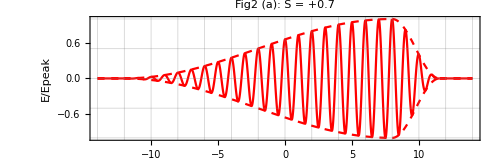

```mathematica
Clear[T1,T2,τ12r,τ12f,τ12,sol,S,c,λ,ω0,T,tpeak]

sol=Solve[{τ12f==τ12-τ12r, S==(τ12r-τ12f)/τ12},{τ12r,τ12f}]
τ12r=sol[[1,1,2]]
τ12f=sol[[1,2,2]]

(* physical parameters *)
c=299792458;(*[m/s]*)
λ=0.8 10^-6;(*[m]*)
ω0=2π c/λ;(*[s-1]*)
T=(2π)/ω0;(*[s]*)
τ12=42;(*[fs] as stated after eq 4*)

S=+0.7;
T1=6τ12r ;
T2=6τ12f;

Tt[t_]:=Piecewise[{{Cos[t/T1]^2 HeavisideTheta[π/2 T1+t],t<0},{Cos[t/T2]^2 HeavisideTheta[π/2 T2-t],t>0}}]

tpeak=8;
Plot[{Tt[2π (tt-tpeak) T 10^15]Cos[ω0 tt  T],Tt[2π (tt-tpeak) T 10^15],-Tt[2π (tt-tpeak) T 10^15]},{tt,-14,+14},Frame->True,FrameLabel->{"t","E/Epeak"},PlotLabel->"Fig2 (a): S = +0.7",PlotStyle->{Red,{Red,Dashed},{Red,Dashed}},AspectRatio->1/3,GridLines->{Table[x,{x,-14,14,2}],{-1,-0.5,0,0.5,1}},ImageSize->500]
```

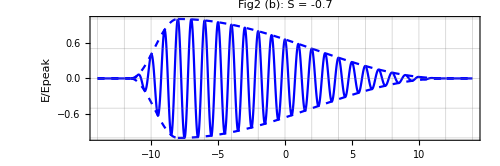

```mathematica
Clear[T1,T2,τ12r,τ12f,τ12,sol,S,c,λ,ω0,T,tpeak]

sol=Solve[{τ12f==τ12-τ12r, S==(τ12r-τ12f)/τ12},{τ12r,τ12f}];
τ12r=sol[[1,1,2]];
τ12f=sol[[1,2,2]];

(* physical parameters *)
c=299792458;(*[m/s]*)
λ=0.8 10^-6;(*[m]*)
ω0=2π c/λ;(*[s-1]*)
T=(2π)/ω0;(*[s]*)
τ12=42;(*[fs] as stated after eq 4*)

S=-0.7;
T1=6τ12r;
T2=6τ12f;

Tt[t_]:=Piecewise[{{Cos[t/T1]^2 HeavisideTheta[π/2 T1+t],t<0},{Cos[t/T2]^2 HeavisideTheta[π/2 T2-t],t>0}}]

tpeak=8;
Plot[{Tt[2π (tt+tpeak) T 10^15]Cos[ω0 tt  T],Tt[2π (tt+tpeak) T 10^15],-Tt[2π (tt+tpeak) T 10^15]},{tt,-14,+14},Frame->True,FrameLabel->{"t","E/Epeak"},PlotLabel->"Fig2 (b): S = -0.7",PlotStyle->{Blue,{Blue,Dashed},{Blue,Dashed}},AspectRatio->1/3,GridLines->{Table[x,{x,-14,14,2}],{-1,-0.5,0,0.5,1}},ImageSize->500]
```